```mathematica
Clear["Global`*"]
```

```mathematica
(*4*4*)(*configuration number*)
f=Import["/Users/mac/Desktop/spin liquid/数据/log_basis_4_4.txt","Table"][[1]];
fz=Import["/Users/mac/Desktop/spin liquid/数据/log_basis_4_4.txt","Table"][[2]];
fzopen=Import["/Users/mac/Desktop/spin liquid/数据/log_basis_4_4.txt","Table"][[3]];
fx=Import["/Users/mac/Desktop/spin liquid/数据/log_basis_4_4.txt","Table"][[4]];
f0=Import["/Users/mac/Desktop/spin liquid/数据/log_basis_4_4.txt","Table"][[5]];
fp=Import["/Users/mac/Desktop/spin liquid/数据/log_basis_4_4.txt","Table"][[6]];
fm=Import["/Users/mac/Desktop/spin liquid/数据/log_basis_4_4.txt","Table"][[7]];
```

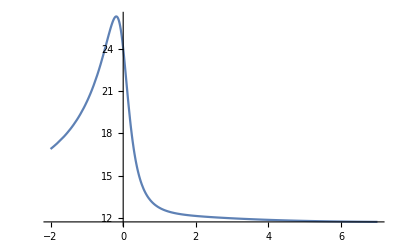

```mathematica
(*atom number*)
Nb=4*4*6;
(*normalization factor*)
Ntot[v_]:=Sum[f[[i+1]]*v^(2*i),{i,0,(Length[f]-1)}];
(*energy*)
E1[v_]:=-Sum[i*f[[i+1]] v^(2*i-1),{i,1,(Length[f]-1)}]/Ntot[v];
E2[v_]:=Sum[(Nb-2*i)/2*f[[i+1]] v^(2*i),{i,0,(Length[f]-1)}]/Ntot[v];
Etot[v_,h_]:=E1[v]+h*E2[v];
(*the monomer number*)
Nmo[v_]:=Sum[2*(1/2*Nb-2*i)*f[[i+1]]*v^(2*i),{i,0,(Length[f]-1)}]/(Nb*Ntot[v]);
Z[v_]:=Sum[(2*fz[[i+1]]-f[[i+1]])*v^(2*i)/Ntot[v],{i,0,(Length[f]-1)}];
X[v_]:=Sum[fx[[i+1]]*v^(2*i)/Ntot[v],{i,0,(Length[f]-1)}];
Zopen[v_]:=Sum[(2*fzopen[[i+1]]-f[[i+1]])*v^(2*i)/Ntot[v],{i,0,(Length[f]-1)}];
Xopen[v_]:=Sum[(f0[[i+1]]*v^(2*i)-fp[[i+1]]*v^(2*i+1)-fm[[i+1]]*v^(2*i-1))/Ntot[v],{i,0,(Length[f]-1)}];
Plot[Etot[v,2],{v,-2,7}]
```

```mathematica
resv={};
Nm={};
Nd={};
resZ={};
resX={};
resZopen={};
resXopen={};
energy={};
VBS={};
Etrival={};
For[h=-2,h<4,h=h+0.03,
a=x/.Last[NMinimize[Etot[x,h],x,Method->"DifferentialEvolution"]];
AppendTo[resv,{h,a}];
AppendTo[Nm,{h,Nmo[a]}];
AppendTo[Nd,{h,(1-Nmo[a])}];
AppendTo[resZ,{h,Z[a]}];
AppendTo[resX,{h,X[a]}];
AppendTo[resZopen,{h,Zopen[a]^2}];
AppendTo[resXopen,{h,Xopen[a]^2}];
AppendTo[energy,{h,Etot[a,h]/Nb}];
AppendTo[VBS,{h,h/4}];
AppendTo[Etrival,{h,h/2}]]
```

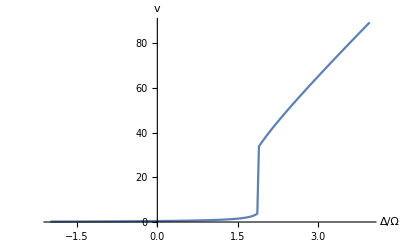

```mathematica
ListLinePlot[{resv},AxesLabel->{HoldForm[Δ/Ω],HoldForm[v]},AxesStyle->Directive[Black,15,FontFamily->"Times"]]
```